```mathematica
pdbFindMoleculeName[name_String,num:(_Integer?Positive):10]:=Module[{query,res},query=XMLObject["Document"][{XMLObject["Declaration"]["Version"->"1.0","Encoding"->"UTF-8"]},XMLElement["orgPdbQuery",{},{XMLElement["queryType",{},{"org.pdb.query.simple.StructTitleQuery"}],XMLElement["struct.title.comparator",{},{"contains"}],XMLElement["struct.title.value",{},{name}]}],{}];
res=URLRead[HTTPRequest["http://www.rcsb.org/pdb/rest/search/",<|"ContentType"->"application/x-www-form-urlencoded","Body"->ExportString[query,"XML"],"Method"->"POST"|>]];
If[!FailureQ[res],res=Import[res];
If[res=!="null",res=DeleteDuplicates[Flatten[res]];
res=Dataset[AssociationThread[{"PDB ID","Title","Structure"},{#,Cases[Import["http://www.rcsb.org/pdb/rest/describePDB?structureId="<>#,"XML"],("title"->t_):>t,∞][[1]],Import["https://files.rcsb.org/download/"<>#<>".pdb","PDB"]}]&/@Take[res,UpTo[num]]],res=Failure["NoResults",<|"MessageTemplate":>"No results found for `name`","MessageParameters"-><|"name"->name|>|>]]];
res]
```

```mathematica
snail=pdbFindMoleculeName["conus textile"]
```

```mathematica
PDBIDList
```

PDBIDList

```mathematica
ProteinData["1WCT","Properties"]
```

ProteinData::notent: "1WCT" is not a known entity, class, or tag for ProteinData. Use ProteinData[] for a list of entities.

ProteinData[1WCT,Properties]

```mathematica
pdb["1wct","structure"]
```

pdb[1wct,structure]

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
fasta=Import["C:\\Users\\AlexandriaTaylor\\Desktop\\Spring 2020\\151(Protein Processing)\\snail.fasta"];
```

```mathematica
fastaElements=Import["C:\\Users\\AlexandriaTaylor\\Desktop\\Spring 2020\\151(Protein Processing)\\snail.fasta","Elements"]
```

{Accession,Data,Description,Header,LabeledData,Length,Plaintext,Sequence}

```mathematica
Import["C:\\Users\\AlexandriaTaylor\\Desktop\\Spring 2020\\151(Protein Processing)\\snail.fasta",""]
```

Import::noelem: The Import element "translation" is not present when importing as FASTA.

```mathematica
ProteinData[snail]
```

ProteinData::notent: Dataset[{<|"PDB ID" -> "1WCT", "Title" -> "A NOVEL CONOTOXIN FROM CONUS TEXTILE WITH UNUSUAL POST-TRANSLATIONAL MODIFICAT…e", "Structure"}, {TypeSystem`Atom[String], TypeSystem`Atom[String], TypeSystem`AnyType}], 2], <|"ID" -> 18683305664122|>] is not a known entity, class, or tag for ProteinData. Use ProteinData[] for a list of entities.

ProteinData[]

```mathematica
ProteinData
```

```mathematica
fastaLabeled2=Import["C:\\Users\\AlexandriaTaylor\\Desktop\\Spring 2020\\151(Protein Processing)\\snail3.fasta","LabeledData"]
```

```mathematica
{"X53283.1 C.texile KK-0 mRNA for conotoxin"->"AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAATGAAGAACCCCGAAGCCTCTAAATTGAACAAGAGGTGGTGCAAACAAAGCGGTGAAATGTGTAATTTGTTAGACCAAAACTGCTGCGACGGCTATTGCATAGTACTTGTCTGCACATAAAACTGCCGTGATGTCTTCTCTTCCCCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG"}/.aminoAcids2Codon
```

{X53283.1 C.texile KK-0 mRNA for conotoxin→AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAATGAAGAACCCCGAAGCCTCTAAATTGAACAAGAGGTGGTGCAAACAAAGCGGTGAAATGTGTAATTTGTTAGACCAAAACTGCTGCGACGGCTATTGCATAGTACTTGTCTGCACATAAAACTGCCGTGATGTCTTCTCTTCCCCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG}

```mathematica
"X53283.1 C.texile KK-0 mRNA for conotoxin"/.%89
```

```mathematica
test2=AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAATGAAGAACCCCGAAGCCTCTAAATTGAACAAGAGGTGGTGCAAACAAAGCGGTGAAATGTGTAATTTGTTAGACCAAAACTGCTGCGACGGCTATTGCATAGTACTTGTCTGCACATAAAACTGCCGTGATGTCTTCTCTTCCCCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG
```

AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAATGAAGAACCCCGAAGCCTCTAAATTGAACAAGAGGTGGTGCAAACAAAGCGGTGAAATGTGTAATTTGTTAGACCAAAACTGCTGCGACGGCTATTGCATAGTACTTGTCTGCACATAAAACTGCCGTGATGTCTTCTCTTCCCCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG

```mathematica
SymbolName[test2]
```

AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAATGAAGAACCCCGAAGCCTCTAAATTGAACAAGAGGTGGTGCAAACAAAGCGGTGAAATGTGTAATTTGTTAGACCAAAACTGCTGCGACGGCTATTGCATAGTACTTGTCTGCACATAAAACTGCCGTGATGTCTTCTCTTCCCCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG

```mathematica
ToCharacterCode[%114]
```

```mathematica
Information[test2]
```

```mathematica
First[%89]
```

X53283.1 C.texile KK-0 mRNA for conotoxin→AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAATGAAGAACCCCGAAGCCTCTAAATTGAACAAGAGGTGGTGCAAACAAAGCGGTGAAATGTGTAATTTGTTAGACCAAAACTGCTGCGACGGCTATTGCATAGTACTTGTCTGCACATAAAACTGCCGTGATGTCTTCTCTTCCCCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG

```mathematica
ChemicalData[aminoAcids]
```

{glycine,L-alanine,L-serine,L-proline,L-valine,L-threonine,L-cysteine,L-isoleucine,L-leucine,L-asparagine,L-aspartic acid,L-glutamine,L-lysine,L-glutamic acid,L-methionine,L-histidine,L-phenylalanine,L-arginine,L-tyrosine,L-tryptophan}

```mathematica
SnailProt1=URLExecute["https://www.uniprot.org/uniprot/P18513.fasta","FASTA"][[1]]
```

MKLTCMMIVAVLFLTAWTFVTADDSGNGLENLFSKAHHEMKNPEASNLNKRCAPFLHPCTFFFPNCCNSYCVQFICL

```mathematica
SnailProt2=URLExecute["https://www.uniprot.org/uniprot/P18512.fasta","FASTA"][[1]]
```

MKLTCMMIVAVLFLTAWTFATADDSSNGLENLFSKAHHEMKNPEASKLNKRCIEQFDPCDMIRHTCCVGVCFLMACI

```mathematica
SnailProt3=URLExecute["https://www.uniprot.org/uniprot/P18511.fasta","FASTA"][[1]]
```

MKLTCMMIVAVLFLTAWTFATADDPRNGLGNLFSNAHHEMKNPEASKLNKRWCKQSGEMCNLLDQNCCDGYCIVLVCT

```mathematica
MainProt=Import["C:\\Users\\AlexandriaTaylor\\Desktop\\Spring 2020\\151(Protein Processing)\\Main.txt","Text"]
```

WCKQSGEMCNLLDQNCCDGYCIVLVCT

```mathematica
SequenceAlignment[MainProt,SnailProt1, SimilarityRules->"BLOSUM62"]
```

{{,MKLTCMMIVAVLFLTA},W,{CKQ,TFVTADD},SG,{,NGLENLFSKAHH},EM,{C,KNPEAS},NL,{,NKRCAPF},L,{DQ,HPCTFFFP},NCC,{DG,NS},YC,{IVLV,VQFI},C,{T,L}}

```mathematica
Flatten[{{"","MKLTCMMIVAVLFLTA"},"W",{"CKQ","TFVTADD"},"SG",{"","NGLENLFSKAHH"},"EM",{"C","KNPEAS"},"NL",{"","NKRCAPF"},"L",{"DQ","HPCTFFFP"},"NCC",{"DG","NS"},"YC",{"IVLV","VQFI"},"C",{"T","L"}}]
```

{,MKLTCMMIVAVLFLTA,W,CKQ,TFVTADD,SG,,NGLENLFSKAHH,EM,C,KNPEAS,NL,,NKRCAPF,L,DQ,HPCTFFFP,NCC,DG,NS,YC,IVLV,VQFI,C,T,L}

```mathematica
Column[{"","MKLTCMMIVAVLFLTA","W","CKQ","TFVTADD","SG","","NGLENLFSKAHH","EM","C","KNPEAS","NL","","NKRCAPF","L","DQ","HPCTFFFP","NCC","DG","NS","YC","IVLV","VQFI","C","T","L"}]
```

MKLTCMMIVAVLFLTA
W
CKQ
TFVTADD
SG

NGLENLFSKAHH
EM
C
KNPEAS
NL

NKRCAPF
L
DQ
HPCTFFFP
NCC
DG
NS
YC
IVLV
VQFI
C
T
L

```mathematica
Apply[StringJoin,{{"","MKLTCMMIVAVLFLTA"},"W",{"CKQ","TFVTADD"},"SG",{"","NGLENLFSKAHH"},"EM",{"C","KNPEAS"},"NL",{"","NKRCAPF"},"L",{"DQ","HPCTFFFP"},"NCC",{"DG","NS"},"YC",{"IVLV","VQFI"},"C",{"T","L"}},{1}]
```

{MKLTCMMIVAVLFLTA,W,CKQTFVTADD,SG,NGLENLFSKAHH,EM,CKNPEAS,NL,NKRCAPF,L,DQHPCTFFFP,NCC,DGNS,YC,IVLVVQFI,C,TL}

```mathematica
SequenceAlignment[MainProt,SnailProt2,SimilarityRules->"BLOSUM62"]
```

{{,MKLTCMMIVAVLFLTA},W,{CKQ,TFATADD},S,{,SN},G,{,LENLFSKAHH},EM,{C,K},N,{L,PEASK},L,{DQN,NKR},C,{,IEQFDP},CD,{GY,MIRHTC},C,{I,VG},V,{,CF},L,{V,MA},C,{T,I}}

```mathematica
Apply[StringJoin,%72,{1}]
```

{MKLTCMMIVAVLFLTA,W,CKQTFATADD,S,SN,G,LENLFSKAHH,EM,CK,N,LPEASK,L,DQNNKR,C,IEQFDP,CD,GYMIRHTC,C,IVG,V,CF,L,VMA,C,TI}

```mathematica
Multicolumn[Apply[StringJoin,{{"","MKLTCMMIVAVLFLTA"},"W",{"CKQ","TFATADD"},"S",{"","SN"},"G",{"","LENLFSKAHH"},"EM",{"C","K"},"N",{"L","PEASK"},"L",{"DQN","NKR"},"C",{"","IEQFDP"},"CD",{"GY","MIRHTC"},"C",{"I","VG"},"V",{"","CF"},"L",{"V","MA"},"C",{"T","I"}},{1}],{Automatic,Automatic},Appearance->"Vertical"]
```

MKLTCMMIVAVLFLTA | G | LPEASK | CD | CF
W | LENLFSKAHH | L | GYMIRHTC | L
CKQTFATADD | EM | DQNNKR | C | VMA
S | CK | C | IVG | C
SN | N | IEQFDP | V | TI

```mathematica
FindClusters[{"MKLTCMMIVAVLFLTA","W","CKQTFATADD","S","SN","G","LENLFSKAHH","EM","CK","N","LPEASK","L","DQNNKR","C","IEQFDP","CD","GYMIRHTC","C","IVG","V","CF","L","VMA","C","TI"}]
```

{{MKLTCMMIVAVLFLTA,CKQTFATADD,G,IVG,V,VMA},{W},{S,SN,LENLFSKAHH,CK,N,L,L},{EM},{LPEASK,IEQFDP},{DQNNKR},{C,CD,C,CF,C},{GYMIRHTC},{TI}}

```mathematica
Commonest[{"MKLTCMMIVAVLFLTA","W","CKQTFATADD","S","SN","G","LENLFSKAHH","EM","CK","N","LPEASK","L","DQNNKR","C","IEQFDP","CD","GYMIRHTC","C","IVG","V","CF","L","VMA","C","TI"}]
```

{C}

```mathematica
Column[{"MKLTCMMIVAVLFLTA","W","CKQTFATADD","S","SN","G","LENLFSKAHH","EM","CK","N","LPEASK","L","DQNNKR","C","IEQFDP","CD","GYMIRHTC","C","IVG","V","CF","L","VMA","C","TI"}]
```

MKLTCMMIVAVLFLTA
W
CKQTFATADD
S
SN
G
LENLFSKAHH
EM
CK
N
LPEASK
L
DQNNKR
C
IEQFDP
CD
GYMIRHTC
C
IVG
V
CF
L
VMA
C
TI

```mathematica
SequenceAlignment[MainProt,SnailProt3,SimilarityRules->"BLOSUM62"]
```

{{,MKLTCMMIVAVLFLTAWTFATADDPRNGLGNLFSNAHHEMKNPEASKLNKR},WCKQSGEMCNLLDQNCCDGYCIVLVCT}

```mathematica
Apply[StringJoin,{{"","MKLTCMMIVAVLFLTAWTFATADDPRNGLGNLFSNAHHEMKNPEASKLNKR"},"WCKQSGEMCNLLDQNCCDGYCIVLVCT"},{1}]
```

{MKLTCMMIVAVLFLTAWTFATADDPRNGLGNLFSNAHHEMKNPEASKLNKR,WCKQSGEMCNLLDQNCCDGYCIVLVCT}

```mathematica
StringJoin[{"MKLTCMMIVAVLFLTAWTFATADDPRNGLGNLFSNAHHEMKNPEASKLNKR","WCKQSGEMCNLLDQNCCDGYCIVLVCT"}]
```

MKLTCMMIVAVLFLTAWTFATADDPRNGLGNLFSNAHHEMKNPEASKLNKRWCKQSGEMCNLLDQNCCDGYCIVLVCT

```mathematica
StringLength["MKLTCMMIVAVLFLTAWTFATADDPRNGLGNLFSNAHHEMKNPEASKLNKRWCKQSGEMCNLLDQNCCDGYCIVLVCT"]
```

78

```mathematica
Characters["MKLTCMMIVAVLFLTAWTFATADDPRNGLGNLFSNAHHEMKNPEASKLNKRWCKQSGEMCNLLDQNCCDGYCIVLVCT"]
```

{M,K,L,T,C,M,M,I,V,A,V,L,F,L,T,A,W,T,F,A,T,A,D,D,P,R,N,G,L,G,N,L,F,S,N,A,H,H,E,M,K,N,P,E,A,S,K,L,N,K,R,W,C,K,Q,S,G,E,M,C,N,L,L,D,Q,N,C,C,D,G,Y,C,I,V,L,V,C,T}

```mathematica
aminoAcids=EntityClass["Chemical","AminoAcids"];
ChemicalData["AminoAcids","Properties"]//Short
```

{AcidityConstants,«98»,Viscosity}

```mathematica
ChemicalData["AminoAcids","Name"]
```

{glycine,L-alanine,L-serine,L-proline,L-valine,L-threonine,L-cysteine,L-isoleucine,L-leucine,L-asparagine,L-aspartic acid,L-glutamine,L-lysine,L-glutamic acid,L-methionine,L-histidine,L-phenylalanine,L-arginine,L-tyrosine,L-tryptophan}

```mathematica
aminoAcids2Codon=AssociationThread[ChemicalData["AminoAcids","Name"]->ChemicalData["AminoAcids","Codons"]]
test=Apply["MKLTCMMIVAVLFLTAWTFVTADDSGNGLENLFSKAHHEMKNPEASNLNKRCAPFLHPCTFFFPNCCNSYCVQFICL"]->ChemicalData["AminoAcids","Codons"]
```

<|glycine→{GGU,GGC,GGA,GGG},L-alanine→{GCU,GCC,GCA,GCG},L-serine→{UCU,UCC,UCA,UCG,AGU,AGC},L-proline→{CCU,CCC,CCA,CCG},L-valine→{GUU,GUC,GUA,GUG},L-threonine→{ACU,ACC,ACA,ACG},L-cysteine→{UGU,UGC},L-isoleucine→{AUU,AUC,AUA},L-leucine→{UUA,UUG,CUU,CUC,CUA,CUG},L-asparagine→{AAU,AAC},L-aspartic acid→{GAU,GAC},L-glutamine→{CAA,CAG},L-lysine→{AAA,AAG},L-glutamic acid→{GAA,GAG},L-methionine→{AUG},L-histidine→{CAU,CAC},L-phenylalanine→{UUU,UUC},L-arginine→{CGU,CGC,CGA,CGG,AGA,AGG},L-tyrosine→{UAU,UAC},L-tryptophan→{UGG}|>

Apply[MKLTCMMIVAVLFLTAWTFVTADDSGNGLENLFSKAHHEMKNPEASNLNKRCAPFLHPCTFFFPNCCNSYCVQFICL]→{{GGU,GGC,GGA,GGG},{GCU,GCC,GCA,GCG},{UCU,UCC,UCA,UCG,AGU,AGC},{CCU,CCC,CCA,CCG},{GUU,GUC,GUA,GUG},{ACU,ACC,ACA,ACG},{UGU,UGC},{AUU,AUC,AUA},{UUA,UUG,CUU,CUC,CUA,CUG},{AAU,AAC},{GAU,GAC},{CAA,CAG},{AAA,AAG},{GAA,GAG},{AUG},{CAU,CAC},{UUU,UUC},{CGU,CGC,CGA,CGG,AGA,AGG},{UAU,UAC},{UGG}}

```mathematica
Normal[test]
```

{Data[MKLTCMMIVAVLFLTAWTFVTADDSGNGLENLFSKAHHEMKNPEASNLNKRCAPFLHPCTFFFPNCCNSYCVQFICL]→{UGG}}

```mathematica
codon2AminoAcid=Join[Join@@(AssociationThread[#[[2]],ConstantArray[#[[1]],Length[#[[2]]]]]&/@Transpose[{ChemicalData["AminoAcids","Name"],ChemicalData["AminoAcids","Codons"]}]),<|"UAA"->"Stop Codon","UAG"->"Stop Codon", "UGA"->"Stop Codon"|>]
```

<|GGU→glycine,GGC→glycine,GGA→glycine,GGG→glycine,GCU→L-alanine,GCC→L-alanine,GCA→L-alanine,GCG→L-alanine,UCU→L-serine,UCC→L-serine,UCA→L-serine,UCG→L-serine,AGU→L-serine,AGC→L-serine,CCU→L-proline,CCC→L-proline,CCA→L-proline,CCG→L-proline,GUU→L-valine,GUC→L-valine,GUA→L-valine,GUG→L-valine,ACU→L-threonine,ACC→L-threonine,ACA→L-threonine,ACG→L-threonine,UGU→L-cysteine,UGC→L-cysteine,AUU→L-isoleucine,AUC→L-isoleucine,AUA→L-isoleucine,UUA→L-leucine,UUG→L-leucine,CUU→L-leucine,CUC→L-leucine,CUA→L-leucine,CUG→L-leucine,AAU→L-asparagine,AAC→L-asparagine,GAU→L-aspartic acid,GAC→L-aspartic acid,CAA→L-glutamine,CAG→L-glutamine,AAA→L-lysine,AAG→L-lysine,GAA→L-glutamic acid,GAG→L-glutamic acid,AUG→L-methionine,CAU→L-histidine,CAC→L-histidine,UUU→L-phenylalanine,UUC→L-phenylalanine,CGU→L-arginine,CGC→L-arginine,CGA→L-arginine,CGG→L-arginine,AGA→L-arginine,AGG→L-arginine,UAU→L-tyrosine,UAC→L-tyrosine,UGG→L-tryptophan,UAA→Stop Codon,UAG→Stop Codon,UGA→Stop Codon|>

```mathematica
aminoAcidAbbreviations=<|"1letter"->AssociationThread[#[[All,1]]->#[[All,2]]],"3letter"->AssociationThread[#[[All,1]]->#[[All,3]]]|>&@{{"glycine","G","Gly"},{"L-alanine","A","Ala"},{"L-serine","S","Ser"},{"L-proline","P","Pro"},{"L-valine","V","Val"},{"L-threonine","T","Thr"},{"L-cysteine","C","Cys"},{"L-leucine","L","Leu"},{"L-asparagine","N","Asn"},{"L-aspartic acid","D","Asp"},{"L-glutamine","Q","Gln"},{"L-lysine","K","Lys"},{"L-glutamic acid","E","Glu"},{"L-methionine","M","Met"},{"L-histidine","H","His"},{"L-phenylalanine","F","Phe"},{"L-arginine","R","Arg"},{"L-tyrosine","Y","Tyr"},{"L-tryptophan","W","Trp"},{"L-isoleucine","I","Ile"},{"Stop Codon","*","*"}};
```

```mathematica
%3
```

<|1letter→<|glycine→G,L-alanine→A,L-serine→S,L-proline→P,L-valine→V,L-threonine→T,L-cysteine→C,L-leucine→L,L-asparagine→N,L-aspartic acid→D,L-glutamine→Q,L-lysine→K,L-glutamic acid→E,L-methionine→M,L-histidine→H,L-phenylalanine→F,L-arginine→R,L-tyrosine→Y,L-tryptophan→W,L-isoleucine→I,Stop Codon→*|>,3letter→<|glycine→Gly,L-alanine→Ala,L-serine→Ser,L-proline→Pro,L-valine→Val,L-threonine→Thr,L-cysteine→Cys,L-leucine→Leu,L-asparagine→Asn,L-aspartic acid→Asp,L-glutamine→Gln,L-lysine→Lys,L-glutamic acid→Glu,L-methionine→Met,L-histidine→His,L-phenylalanine→Phe,L-arginine→Arg,L-tyrosine→Tyr,L-tryptophan→Trp,L-isoleucine→Ile,Stop Codon→*|>|>

```mathematica
aminoAcidAbbreviations2=<|"1letter"->AssociationThread[#[[All,1]]->#[[All,2]]]|>&@{{"glycine","G","Gly"},{"L-alanine","A","Ala"},{"L-serine","S","Ser"},{"L-proline","P","Pro"},{"L-valine","V","Val"},{"L-threonine","T","Thr"},{"L-cysteine","C","Cys"},{"L-leucine","L","Leu"},{"L-asparagine","N","Asn"},{"L-aspartic acid","D","Asp"},{"L-glutamine","Q","Gln"},{"L-lysine","K","Lys"},{"L-glutamic acid","E","Glu"},{"L-methionine","M","Met"},{"L-histidine","H","His"},{"L-phenylalanine","F","Phe"},{"L-arginine","R","Arg"},{"L-tyrosine","Y","Tyr"},{"L-tryptophan","W","Trp"},{"L-isoleucine","I","Ile"},{"Stop Codon","*","*"}};
```

```mathematica
%293
```

<|1letter→<|glycine→G,L-alanine→A,L-serine→S,L-proline→P,L-valine→V,L-threonine→T,L-cysteine→C,L-leucine→L,L-asparagine→N,L-aspartic acid→D,L-glutamine→Q,L-lysine→K,L-glutamic acid→E,L-methionine→M,L-histidine→H,L-phenylalanine→F,L-arginine→R,L-tyrosine→Y,L-tryptophan→W,L-isoleucine→I,Stop Codon→*|>|>

```mathematica
%262
```

<|1letter→<|glycine→G,L-alanine→A,L-serine→S,L-proline→P,L-valine→V,L-threonine→T,L-cysteine→C,L-leucine→L,L-asparagine→N,L-aspartic acid→D,L-glutamine→Q,L-lysine→K,L-glutamic acid→E,L-methionine→M,L-histidine→H,L-phenylalanine→F,L-arginine→R,L-tyrosine→Y,L-tryptophan→W,L-isoleucine→I,Stop Codon→*|>,3letter→<|glycine→Gly,L-alanine→Ala,L-serine→Ser,L-proline→Pro,L-valine→Val,L-threonine→Thr,L-cysteine→Cys,L-leucine→Leu,L-asparagine→Asn,L-aspartic acid→Asp,L-glutamine→Gln,L-lysine→Lys,L-glutamic acid→Glu,L-methionine→Met,L-histidine→His,L-phenylalanine→Phe,L-arginine→Arg,L-tyrosine→Tyr,L-tryptophan→Trp,L-isoleucine→Ile,Stop Codon→*|>|>

```mathematica
%255
```

<|1letter→<|glycine→G,L-alanine→A,L-serine→S,L-proline→P,L-valine→V,L-threonine→T,L-cysteine→C,L-leucine→L,L-asparagine→N,L-aspartic acid→D,L-glutamine→Q,L-lysine→K,L-glutamic acid→E,L-methionine→M,L-histidine→H,L-phenylalanine→F,L-arginine→R,L-tyrosine→Y,L-tryptophan→W,L-isoleucine→I,Stop Codon→*|>,3letter→<|glycine→Gly,L-alanine→Ala,L-serine→Ser,L-proline→Pro,L-valine→Val,L-threonine→Thr,L-cysteine→Cys,L-leucine→Leu,L-asparagine→Asn,L-aspartic acid→Asp,L-glutamine→Gln,L-lysine→Lys,L-glutamic acid→Glu,L-methionine→Met,L-histidine→His,L-phenylalanine→Phe,L-arginine→Arg,L-tyrosine→Tyr,L-tryptophan→Trp,L-isoleucine→Ile,Stop Codon→*|>|>

```mathematica
FileTemplate[Codna]
```

FileTemplate[<|3letter→#1⟦All,1⟧→#1⟦All,2⟧|>]

```mathematica
codon2AA=Query[All,aminoAcidAbbreviations2"1letter"][#]&]@codon2AminoAcid
```

```mathematica
codon3DNA=Query[Codna,All][#]& @codon2AA
```

```mathematica
ClearAll[aa2DNA]
```

```mathematica
aa2DNA=Query[All,Codna]->[Codna,All[#]&]
```

Syntax::sntxf: "Query[All,Codna]→" cannot be followed by "[Codna,All[#]&]".

```mathematica
aa->cc
```

```mathematica
{"G","G","G","G","A","A","A","A","S","S","S","S","S","S","P","P","P","P","V","V","V","V","T","T","T","T","C","C","I","I","I","L","L","L","L","L","L","N","N","D","D","Q","Q","K","K","E","E","M","H","H","F","F","R","R","R","R","R","R","Y","Y","W","*","*","*"}->{"GGU","GGC","GGA","GGG","GCU","GCC","GCA","GCG","UCU","UCC","UCA","UCG","AGU","AGC","CCU","CCC","CCA","CCG","GUU","GUC","GUA","GUG","ACU","ACC","ACA","ACG","UGU","UGC","AUU","AUC","AUA","UUA","UUG","CUU","CUC","CUA","CUG","AAU","AAC","GAU","GAC","CAA","CAG","AAA","AAG","GAA","GAG","AUG","CAU","CAC","UUU","UUC","CGU","CGC","CGA","CGG","AGA","AGG","UAU","UAC","UGG"}
```

{G,G,G,G,A,A,A,A,S,S,S,S,S,S,P,P,P,P,V,V,V,V,T,T,T,T,C,C,I,I,I,L,L,L,L,L,L,N,N,D,D,Q,Q,K,K,E,E,M,H,H,F,F,R,R,R,R,R,R,Y,Y,W,*,*,*}→{GGU,GGC,GGA,GGG,GCU,GCC,GCA,GCG,UCU,UCC,UCA,UCG,AGU,AGC,CCU,CCC,CCA,CCG,GUU,GUC,GUA,GUG,ACU,ACC,ACA,ACG,UGU,UGC,AUU,AUC,AUA,UUA,UUG,CUU,CUC,CUA,CUG,AAU,AAC,GAU,GAC,CAA,CAG,AAA,AAG,GAA,GAG,AUG,CAU,CAC,UUU,UUC,CGU,CGC,CGA,CGG,AGA,AGG,UAU,UAC,UGG}

```mathematica
{"G","G","G","G","A","A","A","A","S","S","S","S","S","S","P","P","P","P","V","V","V","V","T","T","T","T","C","C","I","I","I","L","L","L","L","L","L","N","N","D","D","Q","Q","K","K","E","E","M","H","H","F","F","R","R","R","R","R","R","Y","Y","W","*","*","*"}/.%359
```

{GGU,GGC,GGA,GGG,GCU,GCC,GCA,GCG,UCU,UCC,UCA,UCG,AGU,AGC,CCU,CCC,CCA,CCG,GUU,GUC,GUA,GUG,ACU,ACC,ACA,ACG,UGU,UGC,AUU,AUC,AUA,UUA,UUG,CUU,CUC,CUA,CUG,AAU,AAC,GAU,GAC,CAA,CAG,AAA,AAG,GAA,GAG,AUG,CAU,CAC,UUU,UUC,CGU,CGC,CGA,CGG,AGA,AGG,UAU,UAC,UGG}

```mathematica
Reverse[%360]
```

{UGG,UAC,UAU,AGG,AGA,CGG,CGA,CGC,CGU,UUC,UUU,CAC,CAU,AUG,GAG,GAA,AAG,AAA,CAG,CAA,GAC,GAU,AAC,AAU,CUG,CUA,CUC,CUU,UUG,UUA,AUA,AUC,AUU,UGC,UGU,ACG,ACA,ACC,ACU,GUG,GUA,GUC,GUU,CCG,CCA,CCC,CCU,AGC,AGU,UCG,UCA,UCC,UCU,GCG,GCA,GCC,GCU,GGG,GGA,GGC,GGU}

```mathematica
rulecode={"G","G","G","G","A","A","A","A","S","S","S","S","S","S","P","P","P","P","V","V","V","V","T","T","T","T","C","C","I","I","I","L","L","L","L","L","L","N","N","D","D","Q","Q","K","K","E","E","M","H","H","F","F","R","R","R","R","R","R","Y","Y","W","*","*","*"}->{"GGU","GGC","GGA","GGG","GCU","GCC","GCA","GCG","UCU","UCC","UCA","UCG","AGU","AGC","CCU","CCC","CCA","CCG","GUU","GUC","GUA","GUG","ACU","ACC","ACA","ACG","UGU","UGC","AUU","AUC","AUA","UUA","UUG","CUU","CUC","CUA","CUG","AAU","AAC","GAU","GAC","CAA","CAG","AAA","AAG","GAA","GAG","AUG","CAU","CAC","UUU","UUC","CGU","CGC","CGA","CGG","AGA","AGG","UAU","UAC","UGG"}
```

{G,G,G,G,A,A,A,A,S,S,S,S,S,S,P,P,P,P,V,V,V,V,T,T,T,T,C,C,I,I,I,L,L,L,L,L,L,N,N,D,D,Q,Q,K,K,E,E,M,H,H,F,F,R,R,R,R,R,R,Y,Y,W,*,*,*}→{GGU,GGC,GGA,GGG,GCU,GCC,GCA,GCG,UCU,UCC,UCA,UCG,AGU,AGC,CCU,CCC,CCA,CCG,GUU,GUC,GUA,GUG,ACU,ACC,ACA,ACG,UGU,UGC,AUU,AUC,AUA,UUA,UUG,CUU,CUC,CUA,CUG,AAU,AAC,GAU,GAC,CAA,CAG,AAA,AAG,GAA,GAG,AUG,CAU,CAC,UUU,UUC,CGU,CGC,CGA,CGG,AGA,AGG,UAU,UAC,UGG}

```mathematica
Import["C:\\Users\\AlexandriaTaylor\\Desktop\\Spring 2020\\151(Protein Processing)\\Main.txt"]
```

```mathematica
rulecode/.WCKQSGEMCNLLDQNCCDGYCIVLVCT
```

ReplaceAll::reps: {WCKQSGEMCNLLDQNCCDGYCIVLVCT} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{G,G,G,G,A,A,A,A,S,S,S,S,S,S,P,P,P,P,V,V,V,V,T,T,T,T,C,C,I,I,I,L,L,L,L,L,L,N,N,D,D,Q,Q,K,K,E,E,M,H,H,F,F,R,R,R,R,R,R,Y,Y,W,*,*,*}→{GGU,GGC,GGA,GGG,GCU,GCC,GCA,GCG,UCU,UCC,UCA,UCG,AGU,AGC,CCU,CCC,CCA,CCG,GUU,GUC,GUA,GUG,ACU,ACC,ACA,ACG,UGU,UGC,AUU,AUC,AUA,UUA,UUG,CUU,CUC,CUA,CUG,AAU,AAC,GAU,GAC,CAA,CAG,AAA,AAG,GAA,GAG,AUG,CAU,CAC,UUU,UUC,CGU,CGC,CGA,CGG,AGA,AGG,UAU,UAC,UGG}/.WCKQSGEMCNLLDQNCCDGYCIVLVCT

```mathematica
ToCharacterCode[{"WCKQSGEMCNLLDQNCCDGYCIVLVCT"}]
```

{{87,67,75,81,83,71,69,77,67,78,76,76,68,81,78,67,67,68,71,89,67,73,86,76,86,67,84}}

```mathematica
FromCharacterCode[{{87,67,75,81,83,71,69,77,67,78,76,76,68,81,78,67,67,68,71,89,67,73,86,76,86,67,84}}]
```

```mathematica
{"W","C","K","Q","S","G","E","M","C","N","L","L","D","Q","N","C","C","D","G","Y","C","I","V","L","V","C","T"}/.rulecode
```

{W,C,K,Q,S,G,E,M,C,N,L,L,D,Q,N,C,C,D,G,Y,C,I,V,L,V,C,T}

```mathematica
{"G","G","G","G","A","A","A","A","S","S","S","S","S","S","P","P","P","P","V","V","V","V","T","T","T","T","C","C","I","I","I","L","L","L","L","L","L","N","N","D","D","Q","Q","K","K","E","E","M","H","H","F","F","R","R","R","R","R","R","Y","Y","W","*","*","*"}/.rulecode
```

{GGU,GGC,GGA,GGG,GCU,GCC,GCA,GCG,UCU,UCC,UCA,UCG,AGU,AGC,CCU,CCC,CCA,CCG,GUU,GUC,GUA,GUG,ACU,ACC,ACA,ACG,UGU,UGC,AUU,AUC,AUA,UUA,UUG,CUU,CUC,CUA,CUG,AAU,AAC,GAU,GAC,CAA,CAG,AAA,AAG,GAA,GAG,AUG,CAU,CAC,UUU,UUC,CGU,CGC,CGA,CGG,AGA,AGG,UAU,UAC,UGG}

```mathematica
{"G","G","G","G","A","A","A","A","S","S","S","S","S","S","P","P","P","P","V","V","V","V","T","T","T","T","C","C","I","I","I","L","L","L","L","L","L","N","N","D","D","Q","Q","K","K","E","E","M","H","H","F","F","R","R","R","R","R","R","Y","Y","W","*","*","*"}/.%333
```

{GGU,GGC,GGA,GGG,GCU,GCC,GCA,GCG,UCU,UCC,UCA,UCG,AGU,AGC,CCU,CCC,CCA,CCG,GUU,GUC,GUA,GUG,ACU,ACC,ACA,ACG,UGU,UGC,AUU,AUC,AUA,UUA,UUG,CUU,CUC,CUA,CUG,AAU,AAC,GAU,GAC,CAA,CAG,AAA,AAG,GAA,GAG,AUG,CAU,CAC,UUU,UUC,CGU,CGC,CGA,CGG,AGA,AGG,UAU,UAC,UGG}

```mathematica
aa={"G","G","G","G","A","A","A","A","S","S","S","S","S","S","P","P","P","P","V","V","V","V","T","T","T","T","C","C","I","I","I","L","L","L","L","L","L","N","N","D","D","Q","Q","K","K","E","E","M","H","H","F","F","R","R","R","R","R","R","Y","Y","W","*","*","*"};
```

```mathematica
cc={"GGU","GGC","GGA","GGG","GCU","GCC","GCA","GCG","UCU","UCC","UCA","UCG","AGU","AGC","CCU","CCC","CCA","CCG","GUU","GUC","GUA","GUG","ACU","ACC","ACA","ACG","UGU","UGC","AUU","AUC","AUA","UUA","UUG","CUU","CUC","CUA","CUG","AAU","AAC","GAU","GAC","CAA","CAG","AAA","AAG","GAA","GAG","AUG","CAU","CAC","UUU","UUC","CGU","CGC","CGA","CGG","AGA","AGG","UAU","UAC","UGG"};
```

```mathematica
t=TemplateExpression["aa"->"cc"]
```

TemplateExpression[aa→cc]

```mathematica
TemplateApply[t]
```

aa→cc

```mathematica
"aa"/."aa"->"cc"
```

cc

```mathematica
%285
```

```mathematica
%281
```

<|1letter→<|GGU→G,GGC→G,GGA→G,GGG→G,GCU→A,GCC→A,GCA→A,GCG→A,UCU→S,UCC→S,UCA→S,UCG→S,AGU→S,AGC→S,CCU→P,CCC→P,CCA→P,CCG→P,GUU→V,GUC→V,GUA→V,GUG→V,ACU→T,ACC→T,ACA→T,ACG→T,UGU→C,UGC→C,AUC AUU→I^2,AUA→I,UUA→L,UUG→L,CUU→L,CUC→L,CUA→L,CUG→L,AAU→N,AAC→N,GAU→D,GAC→D,CAA→Q,CAG→Q,AAA→K,AAG→K,GAA→E,GAG→E,AUG→M,CAU→H,CAC→H,UUU→F,UUC→F,CGU→R,CGC→R,CGA→R,CGG→R,AGA→R,AGG→R,UAU→Y,UAC→Y,UGG→W,UAA→*,UAG→*,UGA→*|>|>

```mathematica
%273
```

<|1letter→<|G→GGG,A→GCG,S→AGC,P→CCG,V→GUG,T→ACG,C→UGC,I^2→AUC AUU,I→AUA,L→CUG,N→AAC,D→GAC,Q→CAG,K→AAG,E→GAG,M→AUG,H→CAC,F→UUC,R→AGG,Y→UAC,W→UGG,*→UGA|>|>

```mathematica
%266
```

<|1letter→<|G→GGG,A→GCG,S→AGC,P→CCG,V→GUG,T→ACG,C→UGC,I^2→AUC AUU,I→AUA,L→CUG,N→AAC,D→GAC,Q→CAG,K→AAG,E→GAG,M→AUG,H→CAC,F→UUC,R→AGG,Y→UAC,W→UGG,*→UGA|>|>

```mathematica
{{"G","GGU"},{"G","GGC"},{"G","GGA"},{"G","GGG"},{"A","GCU"},{"A","GCC"},{"A","GCA"},{"A","GCG},{"S","UCU"},{"S","UCC"}{"S","UCA"},{"S","UCG"},{"S","AGU"},{"S","AGC"},{"P","CCU"},{"P","CCC"},{"P","CCA"},{"P","CCG"},{"V","GUU"},{"V","GUC"},{"V","GUA"},{"V","GUG"},{"T","ACU"},{"T","ACC"},{"T","ACA"},{"T","ACG"},{"C","UGU"},{"C","UGC"},{"I","AUU"}{"I","AUC"},{"I","AUA"},{"L","UUA"},{"L","UUG"},{"L","CUU"},{"L","CUC"},{"L","CUA"},{"L","CUG"},{"N","AAU"},{"N","AAC"},{"D","GAU"},{"D","GAC"},{"Q","CAA"},{"Q","CAG"},{"K","AAA"},{"K","AAG"},{"E","GAA"},{"E","GAG"},{"M","AUG"},{"H","CAU"},{"H","CAC"},{"F","UUU"},{"F","UUC"},{"R","CGU"},{"R","CGC"},{"R","CGA"},{"R","CGG"},{"R","AGA"},{"R","AGG"},{"Y","UAU"},{"Y","UAC"},{"W","UGG"},{"*","UAA"},{"*","UAG"},{"*","UGA"}}
```

```mathematica
Values[codon2AA]
```

```mathematica
ReplaceList["WCKQSGEMCNLLDQNCCDGYCIVLVCT"/."aa"->"cc"]
```

ReplaceList[WCKQSGEMCNLLDQNCCDGYCIVLVCT]

```mathematica
trans=codon2AA/.WCKQSGEMCNLLDQNCCDGYCIVLVCT
```

ReplaceAll::reps: {WCKQSGEMCNLLDQNCCDGYCIVLVCT} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

<|GGU→G,GGC→G,GGA→G,GGG→G,GCU→A,GCC→A,GCA→A,GCG→A,UCU→S,UCC→S,UCA→S,UCG→S,AGU→S,AGC→S,CCU→P,CCC→P,CCA→P,CCG→P,GUU→V,GUC→V,GUA→V,GUG→V,ACU→T,ACC→T,ACA→T,ACG→T,UGU→C,UGC→C,AUU→I,AUC→I,AUA→I,UUA→L,UUG→L,CUU→L,CUC→L,CUA→L,CUG→L,AAU→N,AAC→N,GAU→D,GAC→D,CAA→Q,CAG→Q,AAA→K,AAG→K,GAA→E,GAG→E,AUG→M,CAU→H,CAC→H,UUU→F,UUC→F,CGU→R,CGC→R,CGA→R,CGG→R,AGA→R,AGG→R,UAU→Y,UAC→Y,UGG→W,UAA→*,UAG→*,UGA→*|>/.WCKQSGEMCNLLDQNCCDGYCIVLVCT

```mathematica
Rule[Codna,WCKQSGEMCNLLDQNCCDGYCIVLVCT]
```

<|3letter→#1⟦All,1⟧→#1⟦All,2⟧|>→WCKQSGEMCNLLDQNCCDGYCIVLVCT

```mathematica
WCKQSGEMCNLLDQNCCDGYCIVLVCT/.ruled
```

WCKQSGEMCNLLDQNCCDGYCIVLVCT

```mathematica
Normal[codon2AA]
```

```mathematica
Apply[ruled->{WCKQSGEMCNLLDQNCCDGYCIVLVCT}]
```

Apply[{GGU→G,GGC→G,GGA→G,GGG→G,GCU→A,GCC→A,GCA→A,GCG→A,UCU→S,UCC→S,UCA→S,UCG→S,AGU→S,AGC→S,CCU→P,CCC→P,CCA→P,CCG→P,GUU→V,GUC→V,GUA→V,GUG→V,ACU→T,ACC→T,ACA→T,ACG→T,UGU→C,UGC→C,AUU→I,AUC→I,AUA→I,UUA→L,UUG→L,CUU→L,CUC→L,CUA→L,CUG→L,AAU→N,AAC→N,GAU→D,GAC→D,CAA→Q,CAG→Q,AAA→K,AAG→K,GAA→E,GAG→E,AUG→M,CAU→H,CAC→H,UUU→F,UUC→F,CGU→R,CGC→R,CGA→R,CGG→R,AGA→R,AGG→R,UAU→Y,UAC→Y,UGG→W,UAA→*,UAG→*,UGA→*}→{WCKQSGEMCNLLDQNCCDGYCIVLVCT}]

```mathematica
ruled={"GGU"->"G","GGC"->"G","GGA"->"G","GGG"->"G","GCU"->"A","GCC"->"A","GCA"->"A","GCG"->"A","UCU"->"S","UCC"->"S","UCA"->"S","UCG"->"S","AGU"->"S","AGC"->"S","CCU"->"P","CCC"->"P","CCA"->"P","CCG"->"P","GUU"->"V","GUC"->"V","GUA"->"V","GUG"->"V","ACU"->"T","ACC"->"T","ACA"->"T","ACG"->"T","UGU"->"C","UGC"->"C","AUU"->"I","AUC"->"I","AUA"->"I","UUA"->"L","UUG"->"L","CUU"->"L","CUC"->"L","CUA"->"L","CUG"->"L","AAU"->"N","AAC"->"N","GAU"->"D","GAC"->"D","CAA"->"Q","CAG"->"Q","AAA"->"K","AAG"->"K","GAA"->"E","GAG"->"E","AUG"->"M","CAU"->"H","CAC"->"H","UUU"->"F","UUC"->"F","CGU"->"R","CGC"->"R","CGA"->"R","CGG"->"R","AGA"->"R","AGG"->"R","UAU"->"Y","UAC"->"Y","UGG"->"W","UAA"->"*","UAG"->"*","UGA"->"*"}
```

{GGU→G,GGC→G,GGA→G,GGG→G,GCU→A,GCC→A,GCA→A,GCG→A,UCU→S,UCC→S,UCA→S,UCG→S,AGU→S,AGC→S,CCU→P,CCC→P,CCA→P,CCG→P,GUU→V,GUC→V,GUA→V,GUG→V,ACU→T,ACC→T,ACA→T,ACG→T,UGU→C,UGC→C,AUU→I,AUC→I,AUA→I,UUA→L,UUG→L,CUU→L,CUC→L,CUA→L,CUG→L,AAU→N,AAC→N,GAU→D,GAC→D,CAA→Q,CAG→Q,AAA→K,AAG→K,GAA→E,GAG→E,AUG→M,CAU→H,CAC→H,UUU→F,UUC→F,CGU→R,CGC→R,CGA→R,CGG→R,AGA→R,AGG→R,UAU→Y,UAC→Y,UGG→W,UAA→*,UAG→*,UGA→*}

```mathematica
ruled/.Rule->List
```

```mathematica
{{"GGU","G"},{"GGC","G"},{"GGA","G"},{"GGG","G"},{"GCU","A"},{"GCC","A"},{"GCA","A"},{"GCG","A"},{"UCU","S"},{"UCC","S"},{"UCA","S"},{"UCG","S"},{"AGU","S"},{"AGC","S"},{"CCU","P"},{"CCC","P"},{"CCA","P"},{"CCG","P"},{"GUU","V"},{"GUC","V"},{"GUA","V"},{"GUG","V"},{"ACU","T"},{"ACC","T"},{"ACA","T"},{"ACG","T"},{"UGU","C"},{"UGC","C"},{"AUU","I"},{"AUC","I"},{"AUA","I"},{"UUA","L"},{"UUG","L"},{"CUU","L"},{"CUC","L"},{"CUA","L"},{"CUG","L"},{"AAU","N"},{"AAC","N"},{"GAU","D"},{"GAC","D"},{"CAA","Q"},{"CAG","Q"},{"AAA","K"},{"AAG","K"},{"GAA","E"},{"GAG","E"},{"AUG","M"},{"CAU","H"},{"CAC","H"},{"UUU","F"},{"UUC","F"},{"CGU","R"},{"CGC","R"},{"CGA","R"},{"CGG","R"},{"AGA","R"},{"AGG","R"},{"UAU","Y"},{"UAC","Y"},{"UGG","W"},{"UAA","*"},{"UAG","*"},{"UGA","*"}}
```

{{GGU,G},{GGC,G},{GGA,G},{GGG,G},{GCU,A},{GCC,A},{GCA,A},{GCG,A},{UCU,S},{UCC,S},{UCA,S},{UCG,S},{AGU,S},{AGC,S},{CCU,P},{CCC,P},{CCA,P},{CCG,P},{GUU,V},{GUC,V},{GUA,V},{GUG,V},{ACU,T},{ACC,T},{ACA,T},{ACG,T},{UGU,C},{UGC,C},{AUU,I},{AUC,I},{AUA,I},{UUA,L},{UUG,L},{CUU,L},{CUC,L},{CUA,L},{CUG,L},{AAU,N},{AAC,N},{GAU,D},{GAC,D},{CAA,Q},{CAG,Q},{AAA,K},{AAG,K},{GAA,E},{GAG,E},{AUG,M},{CAU,H},{CAC,H},{UUU,F},{UUC,F},{CGU,R},{CGC,R},{CGA,R},{CGG,R},{AGA,R},{AGG,R},{UAU,Y},{UAC,Y},{UGG,W},{UAA,*},{UAG,*},{UGA,*}}

```mathematica
%249/.Rule->List
```

{{GGU,G},{GGC,G},{GGA,G},{GGG,G},{GCU,A},{GCC,A},{GCA,A},{GCG,A},{UCU,S},{UCC,S},{UCA,S},{UCG,S},{AGU,S},{AGC,S},{CCU,P},{CCC,P},{CCA,P},{CCG,P},{GUU,V},{GUC,V},{GUA,V},{GUG,V},{ACU,T},{ACC,T},{ACA,T},{ACG,T},{UGU,C},{UGC,C},{AUU,I},{AUC,I},{AUA,I},{UUA,L},{UUG,L},{CUU,L},{CUC,L},{CUA,L},{CUG,L},{AAU,N},{AAC,N},{GAU,D},{GAC,D},{CAA,Q},{CAG,Q},{AAA,K},{AAG,K},{GAA,E},{GAG,E},{AUG,M},{CAU,H},{CAC,H},{UUU,F},{UUC,F},{CGU,R},{CGC,R},{CGA,R},{CGG,R},{AGA,R},{AGG,R},{UAU,Y},{UAC,Y},{UGG,W},{UAA,*},{UAG,*},{UGA,*}}

```mathematica
Transpose[%362]
```

{{GGU,GGC,GGA,GGG,GCU,GCC,GCA,GCG,UCU,UCC,UCA,UCG,AGU,AGC,CCU,CCC,CCA,CCG,GUU,GUC,GUA,GUG,ACU,ACC,ACA,ACG,UGU,UGC,AUU,AUC,AUA,UUA,UUG,CUU,CUC,CUA,CUG,AAU,AAC,GAU,GAC,CAA,CAG,AAA,AAG,GAA,GAG,AUG,CAU,CAC,UUU,UUC,CGU,CGC,CGA,CGG,AGA,AGG,UAU,UAC,UGG,UAA,UAG,UGA},{G,G,G,G,A,A,A,A,S,S,S,S,S,S,P,P,P,P,V,V,V,V,T,T,T,T,C,C,I,I,I,L,L,L,L,L,L,N,N,D,D,Q,Q,K,K,E,E,M,H,H,F,F,R,R,R,R,R,R,Y,Y,W,*,*,*}}

```mathematica
MatrixForm[%364]
```

```mathematica
Flatten[%362]
```

{GGU,G,GGC,G,GGA,G,GGG,G,GCU,A,GCC,A,GCA,A,GCG,A,UCU,S,UCC,S,UCA,S,UCG,S,AGU,S,AGC,S,CCU,P,CCC,P,CCA,P,CCG,P,GUU,V,GUC,V,GUA,V,GUG,V,ACU,T,ACC,T,ACA,T,ACG,T,UGU,C,UGC,C,AUU,I,AUC,I,AUA,I,UUA,L,UUG,L,CUU,L,CUC,L,CUA,L,CUG,L,AAU,N,AAC,N,GAU,D,GAC,D,CAA,Q,CAG,Q,AAA,K,AAG,K,GAA,E,GAG,E,AUG,M,CAU,H,CAC,H,UUU,F,UUC,F,CGU,R,CGC,R,CGA,R,CGG,R,AGA,R,AGG,R,UAU,Y,UAC,Y,UGG,W,UAA,*,UAG,*,UGA,*}

```mathematica
Sort[%363]
```

{*,*,*,A,A,A,A,AAA,AAC,AAG,AAU,ACA,ACC,ACG,ACU,AGA,AGC,AGG,AGU,AUA,AUC,AUG,AUU,C,C,CAA,CAC,CAG,CAU,CCA,CCC,CCG,CCU,CGA,CGC,CGG,CGU,CUA,CUC,CUG,CUU,D,D,E,E,F,F,G,G,G,G,GAA,GAC,GAG,GAU,GCA,GCC,GCG,GCU,GGA,GGC,GGG,GGU,GUA,GUC,GUG,GUU,H,H,I,I,I,K,K,L,L,L,L,L,L,M,N,N,P,P,P,P,Q,Q,R,R,R,R,R,R,S,S,S,S,S,S,T,T,T,T,UAA,UAC,UAG,UAU,UCA,UCC,UCG,UCU,UGA,UGC,UGG,UGU,UUA,UUC,UUG,UUU,V,V,V,V,W,Y,Y}

```mathematica
WCKQSGEMCNLLDQNCCDGYCIVLVCT/.codon2AA
```

```mathematica
CanonicalName[#]&/@EntityValue["Chemical","Properties"][[1;;10]]
```

{AcidityConstants,AdjacencyMatrix,AlternateNames,AtomCount,AtomPositions,AutoignitionPoint,BeilsteinNumber,BlackStructureDiagram,BoilingPoint,BondCounts}

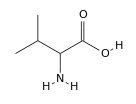
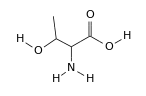
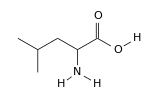
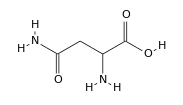
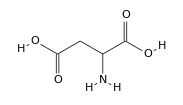
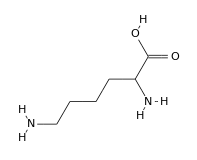
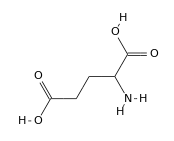
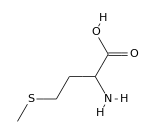
<|glycine→-Graphics-,L-alanine→-Graphics-,L-serine→-Graphics-,L-proline→-Graphics-,L-valine→-Graphics-,L-threonine→-Graphics-,L-cysteine→-Graphics-,L-leucine→-Graphics-,L-asparagine→-Graphics-,L-aspartic acid→-Graphics-,L-glutamine→-Graphics-,L-lysine→-Graphics-,L-glutamic acid→-Graphics-,L-methionine→-Graphics-,DL-histidine→-Graphics-,L-phenylalanine→-Graphics-,L-arginine→-Graphics-,L-tyrosine→-Graphics-,L-tryptophan→-Graphics-,L-isoleucine→-Graphics-|>

```mathematica
EntityValue[#,"BlackStructureDiagram","EntityAssociation"]& @ aminoAcids
```

```mathematica
Values[%160]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

CanonicalName::noent: Chemical is not an entity.

CanonicalName::noent: BondCounts is not an entity.

EntityProperty[CanonicalName[Chemical],CanonicalName[BondCounts]]

```mathematica
EntityClass["WCKQSGEMCNLLDQNCCDGYCIVLVCT",codon2AminoAcid]
```

```mathematica
aminoAcids2Codon
```

<|glycine→{GGU,GGC,GGA,GGG},L-alanine→{GCU,GCC,GCA,GCG},L-serine→{UCU,UCC,UCA,UCG,AGU,AGC},L-proline→{CCU,CCC,CCA,CCG},L-valine→{GUU,GUC,GUA,GUG},L-threonine→{ACU,ACC,ACA,ACG},L-cysteine→{UGU,UGC},L-isoleucine→{AUU,AUC,AUA},L-leucine→{UUA,UUG,CUU,CUC,CUA,CUG},L-asparagine→{AAU,AAC},L-aspartic acid→{GAU,GAC},L-glutamine→{CAA,CAG},L-lysine→{AAA,AAG},L-glutamic acid→{GAA,GAG},L-methionine→{AUG},L-histidine→{CAU,CAC},L-phenylalanine→{UUU,UUC},L-arginine→{CGU,CGC,CGA,CGG,AGA,AGG},L-tyrosine→{UAU,UAC},L-tryptophan→{UGG}|>

```mathematica
Codons
```

Codons

```mathematica
Remove[Codons]
```

Remove::rmptc: Symbol Codons is Protected and cannot be removed.

```mathematica
["GGU"->"glycine","GGC"->"glycine","GGA"->"glycine","GGG"->"glycine","GCU"->"L-alanine","GCC"->"L-alanine","GCA"->"L-alanine","GCG"->"L-alanine","UCU"->"L-serine","UCC"->"L-serine","UCA"->"L-serine","UCG"->"L-serine","AGU"->"L-serine","AGC"->"L-serine","CCU"->"L-proline","CCC"->"L-proline","CCA"->"L-proline","CCG"->"L-proline","GUU"->"L-valine","GUC"->"L-valine","GUA"->"L-valine","GUG"->"L-valine","ACU"->"L-threonine","ACC"->"L-threonine","ACA"->"L-threonine","ACG"->"L-threonine","UGU"->"L-cysteine","UGC"->"L-cysteine","AUU"->"L-isoleucine","AUC"->"L-isoleucine","AUA"->"L-isoleucine","UUA"->"L-leucine","UUG"->"L-leucine","CUU"->"L-leucine","CUC"->"L-leucine","CUA"->"L-leucine","CUG"->"L-leucine","AAU"->"L-asparagine","AAC"->"L-asparagine","GAU"->"L-aspartic acid","GAC"->"L-aspartic acid","CAA"->"L-glutamine","CAG"->"L-glutamine","AAA"->"L-lysine","AAG"->"L-lysine","GAA"->"L-glutamic acid","GAG"->"L-glutamic acid","AUG"->"L-methionine","CAU"->"L-histidine","CAC"->"L-histidine","UUU"->"L-phenylalanine","UUC"->"L-phenylalanine","CGU"->"L-arginine","CGC"->"L-arginine","CGA"->"L-arginine","CGG"->"L-arginine","AGA"->"L-arginine","AGG"->"L-arginine","UAU"->"L-tyrosine","UAC"->"L-tyrosine","UGG"->"L-tryptophan","UAA"->"Stop Codon","UAG"->"Stop Codon","UGA"->"Stop Codon"];
```

Syntax::sntxf: "rulec=" cannot be followed by "[GGU→glycine,GGC→glycine,GGA→glycine,«58»,UAA→Stop Codon,UAG→Stop Codon,UGA→Stop Codon]".

```mathematica
CanonicalName[%222]
```

Codons

```mathematica
SymbolName[Codons]
```

Codons

```mathematica
ToCharacterCode["Codons"]
```

{67,111,100,111,110,115}

```mathematica
Attributes[Codons]
```

{Protected}

```mathematica
Protect[Codons]
```

{Codons}

```mathematica
ToCharacterCode[{"Codons"}]
```

{{67,111,100,111,110,115}}

```mathematica
FromCharacterCode[{{67,111,100,111,110,115}}]
```

{Codons}

```mathematica
StringReplaceList[
```

```mathematica
EntityList[%222]
```

EntityList::noent: EntityClass[<|GGU→glycine,GGC→glycine,GGA→glycine,«58»,UAA→Stop Codon,UAG→Stop Codon,UGA→Stop Codon|>,Codons] is not an entity class.

```mathematica
EntityList[,EntityClass[<|"GGU"->"glycine","GGC"->"glycine","GGA"->"glycine","GGG"->"glycine","GCU"->"L-alanine","GCC"->"L-alanine","GCA"->"L-alanine","GCG"->"L-alanine","UCU"->"L-serine","UCC"->"L-serine","UCA"->"L-serine","UCG"->"L-serine","AGU"->"L-serine","AGC"->"L-serine","CCU"->"L-proline","CCC"->"L-proline","CCA"->"L-proline","CCG"->"L-proline","GUU"->"L-valine","GUC"->"L-valine","GUA"->"L-valine","GUG"->"L-valine","ACU"->"L-threonine","ACC"->"L-threonine","ACA"->"L-threonine","ACG"->"L-threonine","UGU"->"L-cysteine","UGC"->"L-cysteine","AUU"->"L-isoleucine","AUC"->"L-isoleucine","AUA"->"L-isoleucine","UUA"->"L-leucine","UUG"->"L-leucine","CUU"->"L-leucine","CUC"->"L-leucine","CUA"->"L-leucine","CUG"->"L-leucine","AAU"->"L-asparagine","AAC"->"L-asparagine","GAU"->"L-aspartic acid","GAC"->"L-aspartic acid","CAA"->"L-glutamine","CAG"->"L-glutamine","AAA"->"L-lysine","AAG"->"L-lysine","GAA"->"L-glutamic acid","GAG"->"L-glutamic acid","AUG"->"L-methionine","CAU"->"L-histidine","CAC"->"L-histidine","UUU"->"L-phenylalanine","UUC"->"L-phenylalanine","CGU"->"L-arginine","CGC"->"L-arginine","CGA"->"L-arginine","CGG"->"L-arginine","AGA"->"L-arginine","AGG"->"L-arginine","UAU"->"L-tyrosine","UAC"->"L-tyrosine","UGG"->"L-tryptophan","UAA"->"Stop Codon","UAG"->"Stop Codon","UGA"->"Stop Codon"|>,Codons]]
```

```mathematica
EntityProperties[EntityTypeName[EntityProperty[CanonicalName["Chemical"],CanonicalName["BondCounts"]]]]
```

CanonicalName::noent: Chemical is not an entity.

CanonicalName::noent: BondCounts is not an entity.

EntityTypeName::noent: EntityProperty[CanonicalName[Chemical],CanonicalName[BondCounts]] is not an entity.

EntityProperties[EntityTypeName[EntityProperty[CanonicalName[Chemical],CanonicalName[BondCounts]]]]

```mathematica
EntityList[]
```

EntityList::noent: Codon is not an entity class.

EntityList[Codon]

```mathematica
EntityList[aminoAcids]
```

{glycine,L-alanine,L-serine,L-proline,L-valine,L-threonine,L-cysteine,L-leucine,L-asparagine,L-aspartic acid,L-glutamine,L-lysine,L-glutamic acid,L-methionine,DL-histidine,L-phenylalanine,L-arginine,L-tyrosine,L-tryptophan,L-isoleucine}

```mathematica
Entity["Chemical","Glycine"]
```

glycine

```mathematica
aminoAcids
```

amino acids

```mathematica
InputForm[EntityClass["Chemical","AminoAcids"]]
```

EntityClass["Chemical", "AminoAcids"]

codons

WolframAlphaQueryResults

```mathematica
WolframAlpha["WCKQSGEMCNLLDQNCCDGYCIVLVCT",{{"Condons",1},"FormattedData"},PodStates->{"Codon_All reading frames"}]
```

Missing[NotAvailable]

WCKQSGEMCNLLDQNCCDGYCIVLVCT

WolframAlphaQueryResults

```mathematica
First[%174]
```

{{5'-3'  frame 1,UUA | UGA | ACC | CCC | CUG | AUC | CGA | CUC
↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓
L | - | T | P | L | I | R | L
UCU | GGC | GGC | CUU | GGG | GGU | UCA | ACA
↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓
S | G | G | L | G | G | S | T
UCC | AAA | UAA | AGC | GAC
↓ | ↓ | ↓ | ↓ | ↓
S | K | - | S | D},{5'-3'  frame 2,UAU | GAA | CCC | CCC | UGA | UCC | GAC | UCU
↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓
Y | E | P | P | - | S | D | S
CUG | GCG | GCC | UUG | GGG | GUU | CAA | CAU
↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓
L | A | A | L | G | V | Q | H
CCA | AAU | AAA | GCG | ACA
↓ | ↓ | ↓ | ↓ | ↓
P | N | K | A | T},{5'-3'  frame 3,AUG | AAC | CCC | CCU | GAU | CCG | ACU | CUC
↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓
M | N | P | P | D | P | T | L
UGG | CGG | CCU | UGG | GGG | UUC | AAC | AUC
↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓
W | R | P | W | G | F | N | I
CAA | AUA | AAG | CGA | CAG
↓ | ↓ | ↓ | ↓ | ↓
Q | I | K | R | Q},{3'-5'  frame 1,CUG | UCG | CUU | UAU | UUG | GAU | GUU | GAA
↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓
L | S | L | Y | L | D | V | E
CCC | CCA | AGG | CCG | CCA | GAG | AGU | CGG
↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓
P | P | R | P | P | E | S | R
AUC | AGG | GGG | GUU | CAU
↓ | ↓ | ↓ | ↓ | ↓
I | R | G | V | H},{3'-5'  frame 2,UGU | CGC | UUU | AUU | UGG | AUG | UUG | AAC
↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓
C | R | F | I | W | M | L | N
CCC | CAA | GGC | CGC | CAG | AGA | GUC | GGA
↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓
P | Q | G | R | Q | R | V | G
UCA | GGG | GGG | UUC | AUA
↓ | ↓ | ↓ | ↓ | ↓
S | G | G | F | I},{3'-5'  frame 3,GUC | GCU | UUA | UUU | GGA | UGU | UGA | ACC
↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓
V | A | L | F | G | C | - | T
CCC | AAG | GCC | GCC | AGA | GAG | UCG | GAU
↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓
P | K | A | A | R | E | S | D
CAG | GGG | GGU | UCA | UAA
↓ | ↓ | ↓ | ↓ | ↓
Q | G | G | S | -}}

```mathematica
WolframAlpha["AAACATCACCAAAATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTCGTCACGGCTG",{{"AminoAcidSequence",1},"ComputableData"},PodStates->{"AminoAcidSequence__All reading frames"}]
```

{{5'-3'  frame 1,{{{AAA,CAU,CAC,CAA,AAU,GAA,ACU,GAC},{↓,↓,↓,↓,↓,↓,↓,↓},{K,H,H,Q,N,E,T,D}},{{GUG,CAU,GAU,GAU,CGU,UGC,UGU,GCU},{↓,↓,↓,↓,↓,↓,↓,↓},{V,H,D,D,R,C,C,A}},{{GUU,CUU,GAC,CGC,CUG,GAC,AUU,CGU},{↓,↓,↓,↓,↓,↓,↓,↓},{V,L,D,R,L,D,I,R}},{{CAC,GGC},{↓,↓},{H,G}}}},{5'-3'  frame 2,{{{AAC,AUC,ACC,AAA,AUG,AAA,CUG,ACG},{↓,↓,↓,↓,↓,↓,↓,↓},{N,I,T,K,M,K,L,T}},{{UGC,AUG,AUG,AUC,GUU,GCU,GUG,CUG},{↓,↓,↓,↓,↓,↓,↓,↓},{C,M,M,I,V,A,V,L}},{{UUC,UUG,ACC,GCC,UGG,ACA,UUC,GUC},{↓,↓,↓,↓,↓,↓,↓,↓},{F,L,T,A,W,T,F,V}},{{ACG,GCU},{↓,↓},{T,A}}}},{5'-3'  frame 3,{{{ACA,UCA,CCA,AAA,UGA,AAC,UGA,CGU},{↓,↓,↓,↓,↓,↓,↓,↓},{T,S,P,K,-,N,-,R}},{{GCA,UGA,UGA,UCG,UUG,CUG,UGC,UGU},{↓,↓,↓,↓,↓,↓,↓,↓},{A,-,-,S,L,L,C,C}},{{UCU,UGA,CCG,CCU,GGA,CAU,UCG,UCA},{↓,↓,↓,↓,↓,↓,↓,↓},{S,-,P,P,G,H,S,S}},{{CGG,CUG},{↓,↓},{R,L}}}},{3'-5'  frame 1,{{{CAG,CCG,UGA,CGA,AUG,UCC,AGG,CGG},{↓,↓,↓,↓,↓,↓,↓,↓},{Q,P,-,R,M,S,R,R}},{{UCA,AGA,ACA,GCA,CAG,CAA,CGA,UCA},{↓,↓,↓,↓,↓,↓,↓,↓},{S,R,T,A,Q,Q,R,S}},{{UCA,UGC,ACG,UCA,GUU,UCA,UUU,UGG},{↓,↓,↓,↓,↓,↓,↓,↓},{S,C,T,S,V,S,F,W}},{{UGA,UGU},{↓,↓},{-,C}}}},{3'-5'  frame 2,{{{AGC,CGU,GAC,GAA,UGU,CCA,GGC,GGU},{↓,↓,↓,↓,↓,↓,↓,↓},{S,R,D,E,C,P,G,G}},{{CAA,GAA,CAG,CAC,AGC,AAC,GAU,CAU},{↓,↓,↓,↓,↓,↓,↓,↓},{Q,E,Q,H,S,N,D,H}},{{CAU,GCA,CGU,CAG,UUU,CAU,UUU,GGU},{↓,↓,↓,↓,↓,↓,↓,↓},{H,A,R,Q,F,H,F,G}},{{GAU,GUU},{↓,↓},{D,V}}}},{3'-5'  frame 3,{{{GCC,GUG,ACG,AAU,GUC,CAG,GCG,GUC},{↓,↓,↓,↓,↓,↓,↓,↓},{A,V,T,N,V,Q,A,V}},{{AAG,AAC,AGC,ACA,GCA,ACG,AUC,AUC},{↓,↓,↓,↓,↓,↓,↓,↓},{K,N,S,T,A,T,I,I}},{{AUG,CAC,GUC,AGU,UUC,AUU,UUG,GUG},{↓,↓,↓,↓,↓,↓,↓,↓},{M,H,V,S,F,I,L,V}},{{AUG,UUU},{↓,↓},{M,F}}}}}

```mathematica
codon2AA/@StringReplace[(StringPartition["AAACATCACCAAAATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTCGTCACGGCTG",3]),"T"->"U"]
```

{K,H,H,Q,N,E,T,D,V,H,D,D,R,C,C,A,V,L,D,R,L,D,I,R,H,G}

```mathematica
ProteinData["WCKQSGEMCNLLDQNCCDGYCIVLVCT"]
```

ProteinData::notent: "WCKQSGEMCNLLDQNCCDGYCIVLVCT" is not a known entity, class, or tag for ProteinData. Use ProteinData[] for a list of entities.

ProteinData[WCKQSGEMCNLLDQNCCDGYCIVLVCT]

```mathematica
blastprotein=URLExecute["https://blast.ncbi.nlm.nih.gov/Blast.cgi?",{"QUERY"->SnailProt3,"PROGRAM"->"blastp","DATABASE"->"nr","CMD"->"Put"},"Text"];
```

```mathematica
blastsnailinfo=StringCases[blastprotein,"QBlastInfoBegin"~~__~~"QBlastInfoEnd"]
```

{QBlastInfoBegin
    RID = 90892GK6014
    RTOE = 10
QBlastInfoEnd}

```mathematica
ridsnailp=StringSplit[blastsnailinfo][[1,4]]
```

90892GK6014

```mathematica
blastpreturnstatus=URLExecute["https://blast.ncbi.nlm.nih.gov/Blast.cgi?",{"CMD"->"Get","RID"->ridsnailp,"FORMAT_TYPE"->"Tabular","FORMAT_OBJECT"->"status"},"Text"];
```

```mathematica
StringCases[#,"QBlastInfoBegin"~~__~~"QBlastInfoEnd"]&@blastpreturnstatus
```

{QBlastInfoBegin
	Status=READY
QBlastInfoEnd}

```mathematica
blastpReturnCSV=URLExecute["https://blast.ncbi.nlm.nih.gov/Blast.cgi?",{"CMD"->"Get","RID"->ridsnailp,"FORMAT_TYPE"->"CSV","FORMAT_OBJECT"->"Alignment","ALIGNMENT_VIEW"->"Tabular","DESCRIPTIONS"->"3"}]
```

{{Query_6297,P18511.1,100.,78,0,0,1,78,1,78,1.56×10^-51,165,100.},{Query_6297,QFQ61073.1,98.718,78,1,0,1,78,1,78,5.32×10^-51,163,100.},{Query_6297,P0CB09.1,97.436,78,2,0,1,78,1,78,2.22×10^-50,162,100.},{},{}}

```mathematica
Cross1=Import["C:\\Users\\AlexandriaTaylor\\Desktop\\Spring 2020\\151(Protein Processing)\\snail.fasta","LabeledData"]
```

{X53285.1 C.texile KK-2 mRNA for conotoxin→AAACATCACCAAAATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTCGTCACGGCTGATGACTCCGGAAATGGATTGGAAAATCTTTTTTCGAAGGCACATCACGAAATGAAGAACCCCGAAGCCTCTAATTTGAACAAGAGGTGCGCTCCTTTTCTTCACCCTTGTACCTTTTTCTTCCCAAACTGCTGCAACAGCTATTGTGTTCAATTTATCTGCCTATAAAACTACCGTGATGTCTTCTACTCCCCTCTGTGCTACCTGGCTTGATGTTTGATTGGCGCTTGGCCTTCACTGGTTATGAACCCCCCTGATCCGACTCTCTGGCGGCCTTGGGGGTTCAACATCCAAATAAAGCGACAG}

```mathematica
Cross2=Import["C:\\Users\\AlexandriaTaylor\\Desktop\\Spring 2020\\151(Protein Processing)\\snail2.fasta","LabeledData"]
```

{X53284.1 C.textile KK-1 mRNA for conotoxin→AAACATCACCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTCGCCACGGCTGATGACTCCAGCAATGGATTGGAGAATCTTTTTTCGAAGGCACATCACGAAATGAAGAACCCCGAAGCCTCTAAATTGAACAAGAGGTGCATTGAACAATTTGATCCTTGTGAAATGATACGTCACACTTGCTGCGTTGGCGTGTGCTTTCTAATGGCCTGCATCTAAAACTGCCGTGATGTCTTCTACTCCCCTCCTGTGCTACCTGATCTGTGATTGGCGTGGCTTTCACTGGTTAATGAACCCCCCTGATCCGACTCTCTGGAGGCTCGGGGGTTCAACATCCAAATAAAGCGACAG}

```mathematica
Cross3=Import["C:\\Users\\AlexandriaTaylor\\Desktop\\Spring 2020\\151(Protein Processing)\\snail3.fasta","LabeledData"]
```

```mathematica
GenomeLookup[{"X53283.1 C.texile KK-0 mRNA for conotoxin"->"AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAATGAAGAACCCCGAAGCCTCTAAATTGAACAAGAGGTGGTGCAAACAAAGCGGTGAAATGTGTAATTTGTTAGACCAAAACTGCTGCGACGGCTATTGCATAGTACTTGTCTGCACATAAAACTGCCGTGATGTCTTCTCTTCCCCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG"}]
```

GenomeLookup::notent: {"X53283.1 C.texile KK-0 mRNA for conotoxin" -> "AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATG…CTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG"} is not a known entity, class, or tag for GenomeLookup. Use GenomeLookup[] for a list of entities.

GenomeLookup[{X53283.1 C.texile KK-0 mRNA for conotoxin→AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAATGAAGAACCCCGAAGCCTCTAAATTGAACAAGAGGTGGTGCAAACAAAGCGGTGAAATGTGTAATTTGTTAGACCAAAACTGCTGCGACGGCTATTGCATAGTACTTGTCTGCACATAAAACTGCCGTGATGTCTTCTCTTCCCCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG}]

```mathematica
GenomeLookup["AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAATGAAGAACCCCGAAGCCTCTAAATTGAACAAGAGGTGGTGCAAACAAAGCGGTGAAATGTGTAATTTGTTAGACCAAAACTGCTGCGACGGCTATTGCATAGTACTTGTCTGCACATAAAACTGCCGTGATGTCTTCTCTTCCCCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG"]
```

```mathematica
GenomeData[PDB["AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAATGAAGAACCCCGAAGCCTCTAAATTGAACAAGAGGTGGTGCAAACAAAGCGGTGAAATGTGTAATTTGTTAGACCAAAACTGCTGCGACGGCTATTGCATAGTACTTGTCTGCACATAAAACTGCCGTGATGTCTTCTCTTCCCCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG",n]
```

GenomeData::notent: "AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAA…CCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG" is not a known entity, class, or tag for GenomeData. Use GenomeData[] for a list of entities.

GenomeData[AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAATGAAGAACCCCGAAGCCTCTAAATTGAACAAGAGGTGGTGCAAACAAAGCGGTGAAATGTGTAATTTGTTAGACCAAAACTGCTGCGACGGCTATTGCATAGTACTTGTCTGCACATAAAACTGCCGTGATGTCTTCTCTTCCCCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG,n]

```mathematica
GenomeData["AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAATGAAGAACCCCGAAGCCTCTAAATTGAACAAGAGGTGGTGCAAACAAAGCGGTGAAATGTGTAATTTGTTAGACCAAAACTGCTGCGACGGCTATTGCATAGTACTTGTCTGCACATAAAACTGCCGTGATGTCTTCTCTTCCCCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG","FullSequence"]
```

GenomeData::notent: AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAAT…CCCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG is not a known entity, class, or tag for GenomeData. Use GenomeData[] for a list of entities.

GenomeData[AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAATGAAGAACCCCGAAGCCTCTAAATTGAACAAGAGGTGGTGCAAACAAAGCGGTGAAATGTGTAATTTGTTAGACCAAAACTGCTGCGACGGCTATTGCATAGTACTTGTCTGCACATAAAACTGCCGTGATGTCTTCTCTTCCCCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG,FullSequence]

```mathematica
GenomeData["AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAATGAAGAACCCCGAAGCCTCTAAATTGAACAAGAGGTGGTGCAAACAAAGCGGTGAAATGTGTAATTTGTTAGACCAAAACTGCTGCGACGGCTATTGCATAGTACTTGTCTGCACATAAAACTGCCGTGATGTCTTCTCTTCCCCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG","FullSequencePosition"]
```

GenomeData::notent: "AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAA…CCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG" is not a known entity, class, or tag for GenomeData. Use GenomeData[] for a list of entities.

GenomeData[AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAATGAAGAACCCCGAAGCCTCTAAATTGAACAAGAGGTGGTGCAAACAAAGCGGTGAAATGTGTAATTTGTTAGACCAAAACTGCTGCGACGGCTATTGCATAGTACTTGTCTGCACATAAAACTGCCGTGATGTCTTCTCTTCCCCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG,FullSequencePosition]

```mathematica
GenomeData["AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAATGAAGAACCCCGAAGCCTCTAAATTGAACAAGAGGTGGTGCAAACAAAGCGGTGAAATGTGTAATTTGTTAGACCAAAACTGCTGCGACGGCTATTGCATAGTACTTGTCTGCACATAAAACTGCCGTGATGTCTTCTCTTCCCCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG","UniProtAccessions"]
```

GenomeData::notent: "AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAA…CCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG" is not a known entity, class, or tag for GenomeData. Use GenomeData[] for a list of entities.

GenomeData[AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAATGAAGAACCCCGAAGCCTCTAAATTGAACAAGAGGTGGTGCAAACAAAGCGGTGAAATGTGTAATTTGTTAGACCAAAACTGCTGCGACGGCTATTGCATAGTACTTGTCTGCACATAAAACTGCCGTGATGTCTTCTCTTCCCCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG,UniProtAccessions]

```mathematica
GenomeData["AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAATGAAGAACCCCGAAGCCTCTAAATTGAACAAGAGGTGGTGCAAACAAAGCGGTGAAATGTGTAATTTGTTAGACCAAAACTGCTGCGACGGCTATTGCATAGTACTTGTCTGCACATAAAACTGCCGTGATGTCTTCTCTTCCCCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG","BiologicalProcesses"]
```

GenomeData::notent: "AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAA…CCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG" is not a known entity, class, or tag for GenomeData. Use GenomeData[] for a list of entities.

GenomeData[AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAATGAAGAACCCCGAAGCCTCTAAATTGAACAAGAGGTGGTGCAAACAAAGCGGTGAAATGTGTAATTTGTTAGACCAAAACTGCTGCGACGGCTATTGCATAGTACTTGTCTGCACATAAAACTGCCGTGATGTCTTCTCTTCCCCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG,BiologicalProcesses]

```mathematica
GenomeData["AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAATGAAGAACCCCGAAGCCTCTAAATTGAACAAGAGGTGGTGCAAACAAAGCGGTGAAATGTGTAATTTGTTAGACCAAAACTGCTGCGACGGCTATTGCATAGTACTTGTCTGCACATAAAACTGCCGTGATGTCTTCTCTTCCCCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG","InteractingGenes"]
```

GenomeData::notent: "AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAA…CCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG" is not a known entity, class, or tag for GenomeData. Use GenomeData[] for a list of entities.

GenomeData[AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAATGAAGAACCCCGAAGCCTCTAAATTGAACAAGAGGTGGTGCAAACAAAGCGGTGAAATGTGTAATTTGTTAGACCAAAACTGCTGCGACGGCTATTGCATAGTACTTGTCTGCACATAAAACTGCCGTGATGTCTTCTCTTCCCCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG,InteractingGenes]

```mathematica
GenomeData["AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAATGAAGAACCCCGAAGCCTCTAAATTGAACAAGAGGTGGTGCAAACAAAGCGGTGAAATGTGTAATTTGTTAGACCAAAACTGCTGCGACGGCTATTGCATAGTACTTGTCTGCACATAAAACTGCCGTGATGTCTTCTCTTCCCCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG","BiologicalProcesses"]
```

GenomeData::notent: "AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAA…CCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG" is not a known entity, class, or tag for GenomeData. Use GenomeData[] for a list of entities.

GenomeData[AAACATCGCCAAGATGAAACTGACGTGCATGATGATCGTTGCTGTGCTGTTCTTGACCGCCTGGACATTTGCCACGGCTGATGACCCCAGAAATGGATTGGGGAATCTTTTTTCGAATGCACATCACGAAATGAAGAACCCCGAAGCCTCTAAATTGAACAAGAGGTGGTGCAAACAAAGCGGTGAAATGTGTAATTTGTTAGACCAAAACTGCTGCGACGGCTATTGCATAGTACTTGTCTGCACATAAAACTGCCGTGATGTCTTCTCTTCCCCTCTGTGCTACCTGGCTTGATCTTTGATTGGCGCGTGTCGTTCACTGGTTATGAACCCCCCCCCCCCCCCCCCCCCCCCCCTTCCGGCTCTCTGGAGGCCTCGGGGGTTCAACATCCAAATAAAGTGACAG,BiologicalProcesses]